# Комиссаров А.Е. лаб8

```mathematica
Wolfram|Alpha Query
```

```mathematica
1. Базовый рабочий процесс
```

```mathematica
ПРИМЕР 1
```

```mathematica
(*
WolframAlpha["запрос", формат] - отправляет запрос в Wolfram|Alpha и возвращает результат в заданном формате
При использовании формата "Input" дает левую часть уравнения или вывод вычислений на языке Wolfram Language
При использовании формата "Output" дает правую часть уравнения или вывод вычислений на языке Wolfram Language
При использовании формата "FormatData" дает полное уравнение в стандартном синтаксисе языка Wolfram Language
HoldComplete[expr] - полностью защищает expr от стандартного процесса оценки Wolfram Language
Hold[expr] - поддерживает expr в неоцененной форме
HoldComplete используется,когда нужно предотвратить определенные этапы процесса оценки,чему Hold не мешает.
*)
```

```mathematica
WolframAlpha["integrate cos(x+3) from 1pi to 2pi",{{"Input",1},"Input"}]
WolframAlpha["integrate cos(x+3) from 1pi to 2pi",{{"Input",1},"Output"}]
WolframAlpha["integrate cos(x+3) from 1pi to 2pi",{{"Input",1},"FormulaData"}]
```

HoldComplete[∫_(1 π)^(2 π) Cos[3+x]ⅆx]

HoldComplete[2 Sin[3]]

Hold[∫_π^(2 π) Cos[x+3]ⅆx≈0.28224]

```mathematica
ПРИМЕР 2
```

```mathematica
(*ReleaseHold[expr] - удаляет один слой Hold,HoldForm,HoldPattern и HoldComplete (все стандартные неоцененные контейнеры) в выражении expr.
% - дает последний полученный результат*)
```

HoldComplete[Plot[Sin[x^3],{x,1 π,2 π}]]

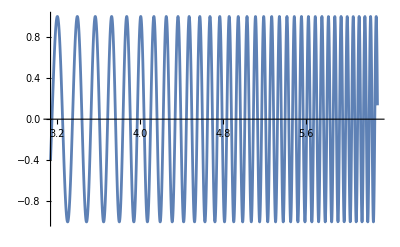

```mathematica
WolframAlpha["integrate sin(x^3) from 1pi to 2pi",{{"Input",1},"FormulaData"}];
WolframAlpha["integrate sin(x^3) from 1pi to 2pi",{{"VisualRepresentationOfTheIntegral",1},"Input"}]
ReleaseHold[%]
```

```mathematica
2. Открытые форматы данных не обязательно похожи на графический результат
```

```mathematica
(*Запрос ниже должен показывать все данные об семейных работниках Японии по сравнению с Филиппинами в виде таблицы*)
```

```mathematica
WolframAlpha["contributing family workers of Japan vs. Philippines",{{"Result",1},"FormattedData"}]
```

Japan | 1.444×10^6 people
Philippines | 2.711×10^6 people
2019 estimates

```mathematica
3. Структура второго аргумента
```

```mathematica
(*{ {"podid","subpodid"}, "property"}
podid - строка, созданная Wolfram|Alpha для идентификации модуля,
subpodid - представляет собой целое число,указывающее положение конкретного результата в модуле,
property - напрямую запрашивает доступные форматы данных для podid*)
```

```mathematica
{WolframAlpha["plot cos(x-1)",{{"Plot",1},"Input"}],WolframAlpha["plot cos(x+1)",{{"Plot",2},"Input"}]}
```

{HoldComplete[Plot[Cos[1-x],{x,2 π,-2 π}]],HoldComplete[Plot[Cos[1+x],{x,-8 π,8 π}]]}

```mathematica
Свободная форма ввода
```

```mathematica
(*Например, чтобы получить доступ к вычислимым данным для интеграла из Примера 1 в задании 1,достаточно щёлкнуть по нему правой кнопкой мыши и выбрать Copy As -> Input data*)
```

```mathematica
∫_(1 π)^(2 π) Cos[3+x]ⅆx
```

2 Sin[3]

# Получение форматов данных программными методами

```mathematica
1. Форматы данных как свойства субмодуля
```

```mathematica
(*Имена программных свойств для различных форматов представляют собой строки,полученные из соответствующих имён меню путем объединения слов в одно целое: Computable data становится "ComputableData",Time series data становится "TimeSeriesData",Input становится "Input".*)
```

```mathematica
WolframAlpha["2+2*2-1",{{"Input",1},"FormulaData"}]
WolframAlpha["2+2*2",{{"Input",1},"ComputableData"}]
```

Hold[2+2 2-1]

Hold[2+2 2]

```mathematica
2. Определение доступных форматов
```

```mathematica
(*Форматы данных,доступные для конкретного субмодуля,содержатся в свойстве «DataFormats» каждого субмодуля.Это свойство можно вычислить так же,как и любое другое свойство вложенного модуля.*)
```

```mathematica
WolframAlpha["contributing family workers of Japan vs. Philippines",{All,"DataFormats"}]
```

{{{Input,1},DataFormats}→{Plaintext,Input,ComputableData,FormattedData},{{Result,1},DataFormats}→{Plaintext,ComputableData,FormattedData,NumberData,QuantityData},{{Comparisons:ContributingFamilyWorkers:WorldDevelopmentData,1},DataFormats}→{Plaintext,ComputableData,FormattedData,NumberData,QuantityData},{{History:ContributingFamilyWorkers:WorldDevelopmentData,1},DataFormats}→{ComputableData,FormattedData,TimeSeriesData},{{EmploymentCharacteristics:WorldDevelopmentData,1},DataFormats}→{Plaintext,ComputableData,FormattedData,NumberData,QuantityData}}

```mathematica
3. Прямые запросы данных
```

```mathematica
(*В WolframAlpha["podid","property"]
podid - строка, созданная Wolfram|Alpha для идентификации модуля
property - напрямую запрашивает доступные форматы данных для podid*)
```

```mathematica
WolframAlpha["2+2*2",{All,{"Output","FormulaData"}}]
```

{{{Result,1},Output}→HoldComplete[6],{{Input,1},FormulaData}→Hold[2+2 2],{{Result,1},FormulaData}→Hold[6]}

```mathematica
(*Можно запрашивать определенные форматы из определенного подмодуля.В случае,если конкретный формат недоступен,мы все равно получаем правило для него с правой частью Missing["NotAvailable"]:*)
```

```mathematica
WolframAlpha["2+2*2",{{"Result",1},{"Output","FormulaData"}}]
```

{{{Result,1},Output}→HoldComplete[6],{{Result,1},FormulaData}→Hold[6]}

# Примеры открытых данных

```mathematica
1 Величины и числа
```

```mathematica
(*  Показывает все данные об семейных работниках Японии по сравнению с Филиппинами в виде таблицы *)
WolframAlpha["contributing family workers of Japan vs. Philippines",{{"Result",1},"Output"}]
```

Japan | 1.438×10^6 people
Philippines | 2.713×10^6 people
2019 estimates

```mathematica
(*  Показывает все данные об семейных работниках Японии по сравнению с Филиппинами в виде списка *)
StringSplit[WolframAlpha["contributing family workers of Japan vs. Philippines",{{"Result",1},"Output"}],"\n"]
```

{{Japan,1.438×10^6 people},{Philippines,2.713×10^6 people}}

```mathematica
(*  Показывает все данные об семейных работниках Японии по сравнению с Филиппинами в виде списка числовых значений*)
WolframAlpha["contributing family workers of Japan vs. Philippines",{{"Result",1},"Numeric"}]
```

{1.438×10^6,2.713×10^6}

```mathematica
(*  Показывает данные об семейных работниках Японии по сравнению с Филиппинами в виде списка количесвтвенных данных*)
WolframAlpha["contributing family workers of Japan vs. Philippines",{{"Result",1},"ComputableData"}]
```

{1.438×10^6 people,2.713×10^6 people}

```mathematica
3. Временные ряды
```

```mathematica
(*выводим список id для всех под, чтобы знать по чему выводить график*)
WolframAlpha["contributing family workers of Japan vs. Philippines", "PodIDs"]
```

{Input,Result,Comparisons:ContributingFamilyWorkers:WorldDevelopmentData,History:ContributingFamilyWorkers:WorldDevelopmentData,EmploymentCharacteristics:WorldDevelopmentData}

```mathematica
(* Показывает график данных об семейных работниках Японии по сравнению с Филиппинами в графическом виде *)
WolframAlpha["contributing family workers of Japan vs. Philippines",{{"Result",1},"ComputableData"},IncludePods->"Image:TimelinePlot"]
```

WolframAlphaQueryResults

```mathematica
4. Формулы
```

```mathematica
(*Поиск формулы пифагора и вывод информации о её теореме*)
WolframAlpha[Pythagorean theorem,{{"Result",1},"PlainText"}];
```

Hold[a^2+b^2==c^2] | 
Hold[c] | hypotenuse
Hold[a] | first side length
Hold[b] | second side length

```mathematica
5. Звуки
```

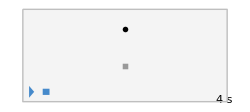
{WolframAlphaQueryResults -Graphics-}

```mathematica
(*При помощи WolframAlpha находим ноты в до мажоре и строим их в пределах 1-2 октавы в секвенсере*)
WolframAlpha["Musical notes in C major",{{"Result",1},"PlainText"}];
(*При помощи WolframAlpha находим ноты в си миноре и строим их в пределах 1-2 октавы в нотная тетради*)
WolframAlpha["Musical notes in A minor within 1-2 octaves",{{"Result",1},"Image"},IncludePods->"Image:MusicNotes"};
```